```mathematica
HydrogenRadial[n_,l_,r_]:= 2/n^2 √(((n-l-1)!)/((n+l)!))(2 r/n)^l Exp[-r/n] LaguerreL[n-l-1,2l+1,2r/n]
HydrogenTheta[l_,m_,th_]:= LegendreP[l,Abs[m],Cos[th]] √((2l+1)/(4Pi) ((l-Abs[m])!)/((l+Abs[m])!))
```

```mathematica
HydrogenTheta[5,2,1.645]
```

0.122892

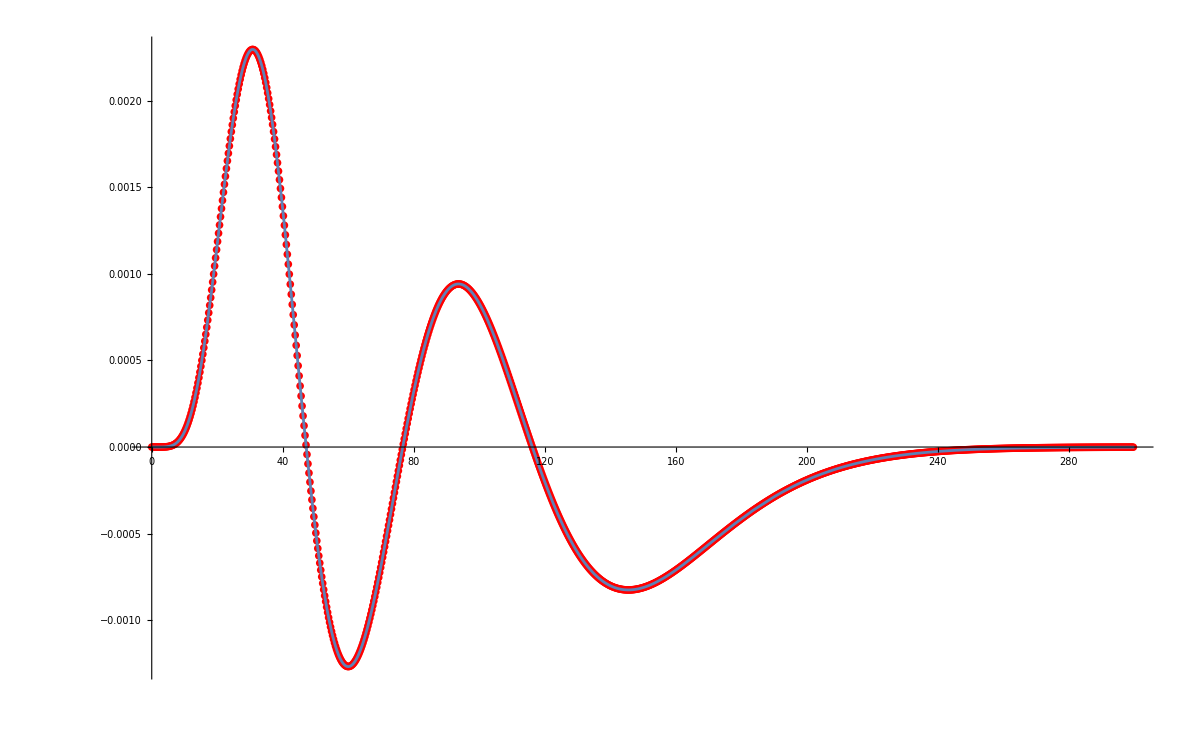

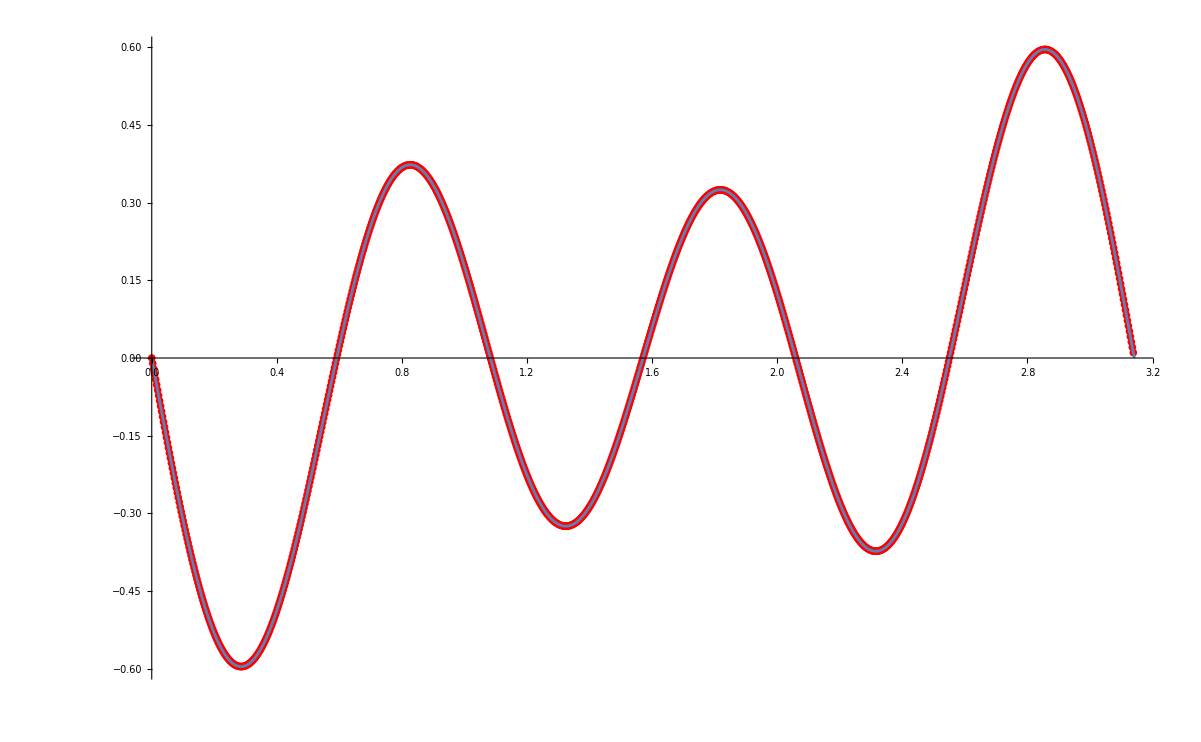

1.

```mathematica
n=10;
l=6;
m=-1;
HydrogenRadialCpp=Import["output/hydrogen.r_wf","Table"];
HydrogenThetaCpp=Import["output/hydrogen.th_wf","Table"];

Show[
ListPlot[HydrogenRadialCpp,PlotStyle->Red,PlotRange->All],
Plot[HydrogenRadial[n,l,r],{r,0,3 n^2},PlotRange->All]]

Show[
ListPlot[HydrogenThetaCpp,PlotStyle->Red,PlotRange->All],
Plot[HydrogenTheta[l,m,th],{th,0,Pi},PlotRange->All]]


∫_0^(3.0 n^2) (HydrogenRadial[n,l,r])^2 r^2 ⅆr
```